# Masterthesis Plots

Define plot style

```mathematica
baseStyle:={BaseStyle->{FontFamily->"Latin Modern Math"}}
defaultPlotOptions:={ImageSize->Medium,baseStyle,PlotTheme->{"Frame","Grid"},GridLines->None};
```

Discrete (sampled) sine

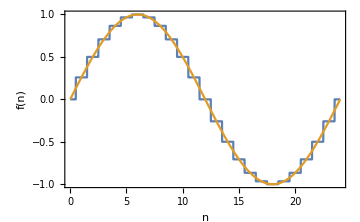

```mathematica
nn=24;
lookupPlot=Plot[{Sin[Round[t]/nn 2Pi],Sin[t/nn*2Pi]},{t,0,nn},Evaluate@defaultPlotOptions,
Exclusions->None,FrameTicks->{{Automatic,Automatic},{Automatic,Table[{i,(2Pi*i)/nn},{i,0,nn,nn/4}]}},FrameLabel->{"n","f(n)"}]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/table-lookup.pdf",lookupPlot,"PDF"];
```

```mathematica
ColorFunction->Function[{x,y},Hue[y]]
```

ColorFunction→Function[{x,y},Hue[y]]

Sine wave spectrum

```mathematica
ListPlot[Im[Fourier[Table[N[Sin[t/n*2Pi]],{t,0,n-1}]]],PlotRange->Full,Filling->Axis,Evaluate@defaultPlotOptions]
```

Table::iterb: Iterator {t,0,-1+n} does not have appropriate bounds.

Fourier::fftl: Argument Table[N[Sin[(t 2 π)/n]],{t,0,-1+n}] is not a non-empty list or rectangular array of numeric quantities.

Table::iterb: Iterator {t,0,-1.+n} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Fourier::fftl: Argument Table[N[Sin[(t 2. 3.141592653589793)/n]],{t,0,-1.+n}] is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument Table[N[Sin[(t 2. 3.14159)/n]],{t,0.,-1.+n}] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

ListPlot::lpn: Im[Fourier[Table[N[Sin[(t Power[«2»]) 2. 3.14159]],{t,0.,-1.+n}]]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Im[Fourier[Table[N[Sin[(t 2 π)/n]],{t,0,-1+n}]]],PlotRange→Full,Filling→Axis,{ImageSize→Medium,{BaseStyle→{FontFamily→Latin Modern Math}},PlotTheme→{Frame,Grid},GridLines→None}]

Wavetable and spectrum

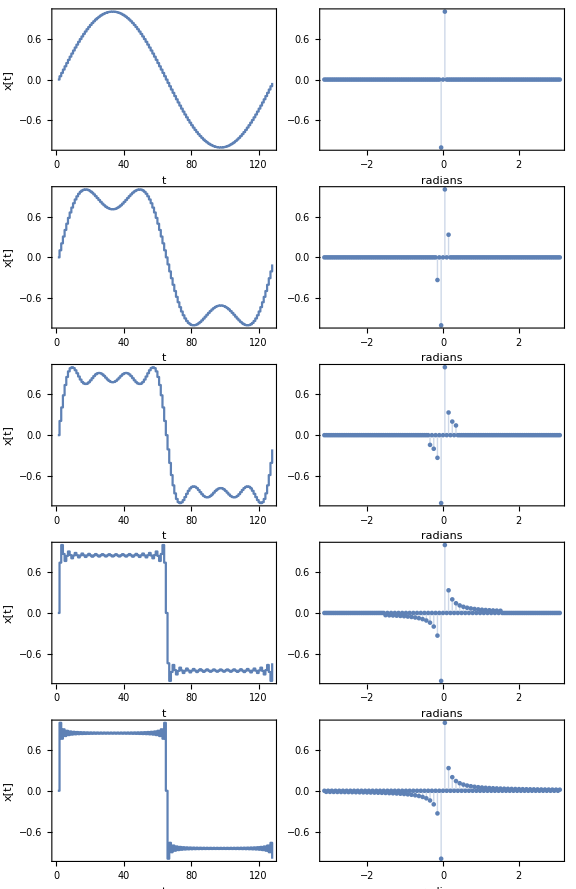

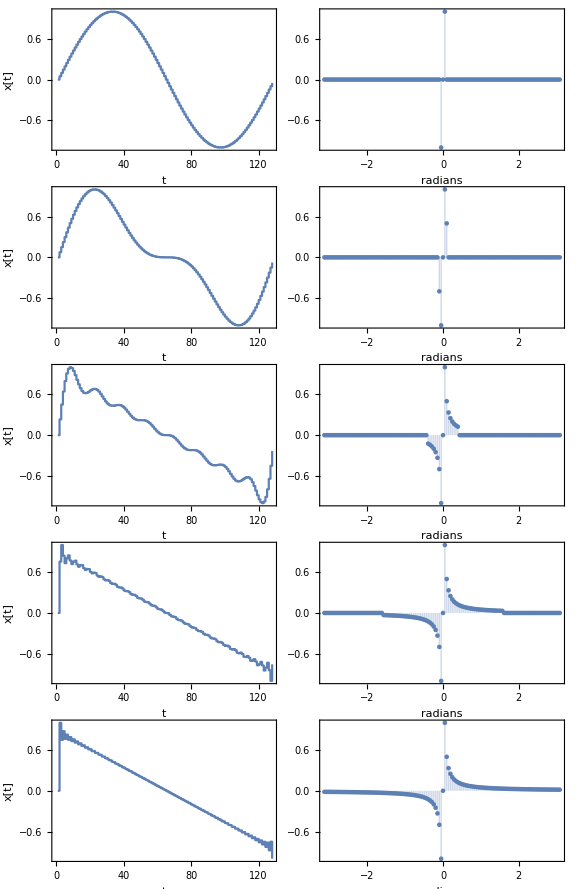

```mathematica
n=128;
sr=64;
dt=1/sr;
df=sr/n;
saw[h_]:=RotateRight[Table[If[k==0||Abs[k]>h,0,I/k],{k,-n/2,n/2-1}],n/2];
sqr[h_]:=RotateRight[Table[If[EvenQ[k]||k==0||Abs[k]>h,0,I/k],{k,-n/2,n/2-1}],n/2];
(* the zeroth element of a list contains its type *)
radians=2 Pi/n Range[-n/2,n/2-1];
plotsSaw =Table[{
ListLinePlot[2Rescale[Re[InverseFourier[saw[k]]]]-1,PlotRange->{{0,n},{-1,1}},InterpolationOrder->0,FrameLabel->{"t","x[t]"},Evaluate@defaultPlotOptions],
ListPlot[MapThread[List,{radians,Im[RotateRight[saw[k],n/2]]}],PlotRange->Full, Filling->Axis,FrameLabel->{"radians"},Evaluate@defaultPlotOptions]
},{k,{1,2,8,n/4,n}}];
plotsSquare =Table[{
ListLinePlot[2Rescale[Re[InverseFourier[sqr[k]]]]-1,PlotRange->Full,InterpolationOrder->0,FrameLabel->{"t","x[t]"},Evaluate@defaultPlotOptions],
ListPlot[MapThread[List,{radians,Im[RotateRight[sqr[k],n/2]]}],PlotRange->Full, Filling->Axis,FrameLabel->{"radians"},Evaluate@defaultPlotOptions]
},{k,{1,4,8,n/4,n}}];
sqrPlot=Show[GraphicsGrid[plotsSquare,Frame->False,ImageSize->Large,Spacings->0]]
sawPlot=Show[GraphicsGrid[plotsSaw,Frame->False,ImageSize->Large,Spacings->0]]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/sqr-table.pdf",sqrPlot,"PDF"];
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/saw-table.pdf",sawPlot,"PDF"];
```

Ration between input levels and db scale

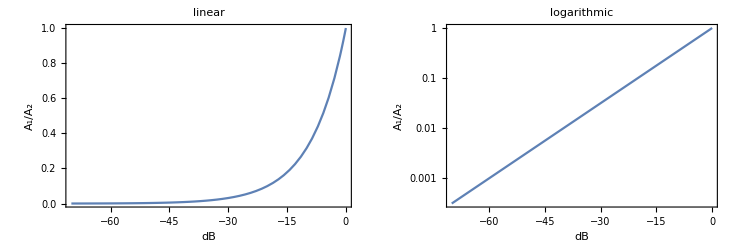

```mathematica
dB[lev_] := 20 Log10[lev/1];
dbPlot=GraphicsRow[{
Plot[10^(d/20),{d,0,-70},PlotLabel->"linear", PlotRange->{{0,-70},{0,1}},FrameLabel->{"dB","A_1/A_2"}, RotateLabel->False,Evaluate@defaultPlotOptions],LogPlot[10^(d/20),{d,0,-70},PlotLabel->"logarithmic",PlotRange->{{0,-70},{0,1}},FrameLabel->{"dB","A_1/A_2"}, RotateLabel->False,Evaluate@defaultPlotOptions]
},Spacings->0]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/db.pdf",dbPlot,"PDF"];
```

Table Interpolation

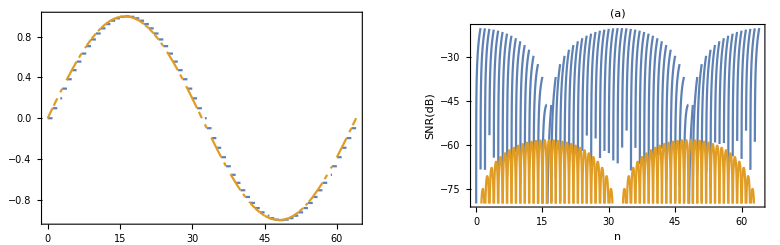

-28.0471

-20.3103

-64.125

-58.394

```mathematica
nn=64; (* Nr. of samples *)
s[n_]:=Sin[n/nn*2Pi];(* pure sine *)
sRound[n_]:=Sin[Floor[n]/nn*2Pi]; (* sine zero-degree interpolation *)
sInt[n_]:=s[Floor[n]]+(s[Floor[n]+1]-s[Floor[n]])(n-Floor[n]);(* sine with linear interpolation *)

sampledSine=Plot[{sRound[x],sInt[x]},{x,0,nn},
PlotRange->{{0,nn},{-1,1}},Evaluate@defaultPlotOptions];
(* error plot *)
interpolationErrorPlot=Plot[{dB[Abs[s[x]-sRound[x]]],dB[Abs[s[x]-sInt[x]]]},{x,0,nn},PlotRange->{{0,nn},{0,-80}},FrameLabel->{"n","SNR(dB)"},Evaluate@defaultPlotOptions,PlotLabel->"(a)"];
GraphicsRow[{sampledSine,interpolationErrorPlot}]
t1:=Table[s[n]-sRound[n]//N,{n,0,nn,1/nn}];
t2:=Table[s[n]-sInt[n]//N,{n,0,nn,1/nn}]; 
dB[RootMeanSquare[t1]]
dB[Max[t1]]
dB[RootMeanSquare[t2]]
dB[Max[t2]]
```

```mathematica
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/interpolation-error.pdf",interpolationErrorPlot,"PDF"]
```

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/interpolation-error.pdf

Aliasing

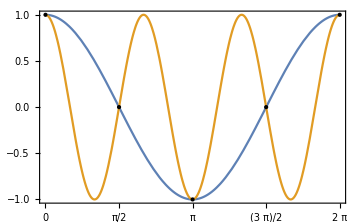

```mathematica
aliasPlot=Plot[{Cos[x],Cos[3x]},{x,0,2Pi},GridLines->{{Pi,2Pi},{-1,-.5,0,.5,1}},Epilog->{PointSize->Large,Point[Table[{n ,Cos[n]},{n,0,2Pi,Pi/2}]]},
FrameTicks->{{Automatic,Automatic},{Table[n,{n,0,2Pi,Pi/2}],Automatic}},Evaluate@defaultPlotOptions]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/aliasing.pdf",aliasPlot,"PDF"];
```

Theoretical SNR for single and double precision floating point values

```mathematica
(* machine epsilon, the negative exponent is the length of the significand (old mantissa) *)
N[dB[2^-24]]
N[dB[2^-53]]
N[dB[1/(2^(16-1))]]
```

-144.494

-319.092

-90.309

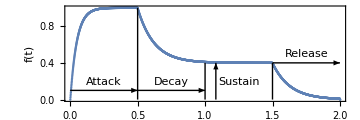

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/adsr.pdf

```mathematica
levels={1,0.4,0};
fs = 1024;
dur[t_]:=Round[t fs];
duration={2,dur[.5],dur[1],dur[0.5]};
gain={0.02,0.008,0.0075};
aa = Table[0,Total[duration]];
Do[aa[[n]]=levels[[1]]gain[[1]]+(1-gain[[1]])aa[[n-1]],{n,duration[[1]],duration[[2]]}];
Do[aa[[n]]=levels[[2]]gain[[2]]+(1-gain[[2]])aa[[n-1]],{n,duration[[2]],duration[[2]]+duration[[3]]}];
Do[aa[[n]]=levels[[3]]gain[[3]]+(1-gain[[3]])aa[[n-1]],{n,duration[[2]]+duration[[3]],duration[[2]]+duration[[3]]+duration[[4]]}];
secTicks:=Range[Length[aa]]/fs;
adsr=ListPlot[Transpose@{secTicks,aa},AspectRatio->1/3,FrameLabel->{"t in seconds","f(t)"},Epilog->{Arrowheads[{-Small,Small}],
 Arrow[{{0,.1},{.5,.1}}],Text["Attack",Scaled[{0.14,0.2}]],
Arrow[{{.5,.1},{1,.1}}],Text["Decay",Scaled[{0.38,0.2}]],
Arrow[{{1.08,0},{1.08,.4}}],Text["Sustain",Scaled[{0.62,0.2}]],
Arrow[{{1.5,.4},{2,.4}}],Text["Release",Scaled[{0.86,.5}]],
Line[{{0.5,0},{0.5,1}}],Line[{{1.0,0},{1.0,0.4}}],Line[{{1.5,0},{1.5,0.4}}]
},Evaluate@defaultPlotOptions]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/adsr.pdf",adsr,"PDF"]
```

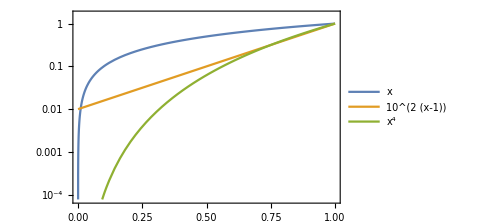

```mathematica
LogPlot[{x,10^(2(x-1)),x^4},{x,0,1},PlotLegends->"Expressions",Evaluate@defaultPlotOptions]
```

`ListSpectrumReal` returns the real spectrum of the given list

```mathematica
ListSpectrumReal[data_]:=Module[{scale,half,len},
len=Length@data;
scale=1/Sqrt[len/4];
half=If[EvenQ[len],Floor[len/2],Floor[len/2]+1];
scale Abs@Fourier[data[[All,2]],FourierParameters->{1,-1}][[;;half]]
];
```

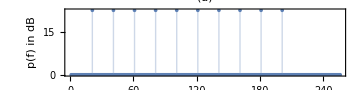

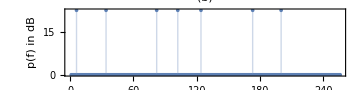

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/harmonic-spectrum.pdf

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/inharmonic-spectrum.pdf

```mathematica
sr=512;
harmonics=Table[20x,{x,1,10}];
inharmonics={33,123,81,5,101,172,199};
hData = Table[{t,Sum[Sin[2Pi fr t] ,{fr,harmonics}]//N},{t,0,1-1/sr,1/sr}];
inhData = Table[{t,Sum[Sin[2Pi fr t],{fr,inharmonics}]//N},{t,0,1-1/sr,1/sr}];
harmonicSpectrum=ListPlot[ListSpectrumReal[hData],Evaluate@defaultPlotOptions, PlotRange->All,Filling->Bottom,
AspectRatio->1/4,
ImageSize->Large,
Frame->True,FrameTicks->{{Automatic,None}, {Automatic,harmonics}},
FrameLabel->{"f in Hz","p(f) in dB"},
PlotLabel->"(a)"]
inharmonicSpectrum=ListPlot[ListSpectrumReal[inhData],Evaluate@defaultPlotOptions, PlotRange->All,Filling->Bottom,AspectRatio->1/4,
ImageSize->Large,
Frame->True,FrameTicks->{{Automatic,None}, {Automatic,inharmonics}},
FrameLabel->{"f in Hz","p(f) in dB"},PlotLabel->"(b)"]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/harmonic-spectrum.pdf",harmonicSpectrum,"PDF"]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/inharmonic-spectrum.pdf",inharmonicSpectrum,"PDF"]
```

Ring Modulation & FM Synthesis

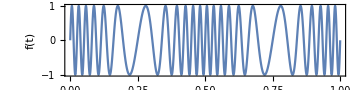

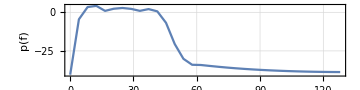

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-wave.pdf

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-spectrum.pdf

```mathematica
sr=256;
fmWavePlot=Plot[Sin[2Pi 24 t+8Sin[2Pi 2t]]//N,{t,0,1},AspectRatio->1/4,FrameLabel->{"t in s","f(t)"},Evaluate@defaultPlotOptions]
(* check the periodgram parameters *)
fmSpectrumPlot=Periodogram[Table[Sin[2Pi 24 t+8Sin[2Pi 2t]]//N,{t,0,1-1/sr,1/sr}],64,32,HammingWindow,PlotRange->All,SampleRate->sr,AspectRatio->1/4,Frame->True,FrameLabel->{"f in Hz", "p(f)"},GridLines->Automatic,Evaluate@baseStyle]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-wave.pdf",fmWavePlot,"PDF"]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/fm-spectrum.pdf",fmSpectrumPlot,"PDF"]
```

### Filter

Filter band example

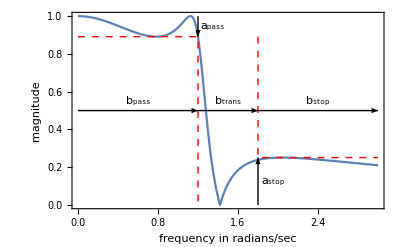

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/filter-bands.pdf

```mathematica
Subscript[w, pass]=1.2;
Subscript[w, stop]=1.8;
Subscript[a, pass]=1;
Subscript[a, stop]=12;
Subscript[g, pass]=10^(-Subscript[a, pass]/20)//N;
Subscript[g, stop]=10^(-Subscript[a, stop]/20)//N;
tf=EllipticFilterModel[{"Lowpass",{Subscript[w, pass],Subscript[w, stop]},{Subscript[a, pass],Subscript[a, stop]}}];
Module[{xmax},xmax=3;
bandPlot=Plot[Abs[tf[I*ω]],{ω,0,xmax},PlotRange->All,Epilog->{
{Red,Dashed,Line[{{0,Subscript[g, pass]},{Subscript[w, pass],Subscript[g, pass]},{Subscript[w, pass],0}}],Line[{{Subscript[w, stop],Subscript[g, pass]},{Subscript[w, stop],Subscript[g, stop]},{xmax,Subscript[g, stop]}}]},
{Arrowheads[{-Small,Small}],Arrow[{{0,.5},{Subscript[w, pass],.5}}],Arrow[{{Subscript[w, pass],.5},{Subscript[w, stop],.5}}],Arrow[{{Subscript[w, stop],.5},{xmax,.5}}],
Arrow[{{Subscript[w, pass],1},{Subscript[w, pass],Subscript[g, pass]}}],Arrow[{{Subscript[w, stop],0},{Subscript[w, stop],Subscript[g, stop]}}]},
Text["b_pass",{Subscript[w, pass]/2,.55}],Text["b_trans",{xmax/2,.55}],Text["b_stop",{Subscript[w, stop]+(xmax-Subscript[w, stop])/2,.55}],
Text["a_pass",{Subscript[w, pass]+0.15,1-(1-Subscript[g, pass])/2}],
Text["a_stop",{Subscript[w, stop]+0.15,Subscript[g, stop]/2}]
},Evaluate@baseStyle,Frame->{{True,False},{True,False}},FrameLabel->{"frequency in radians/sec","magnitude"}]
]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/filter-bands.pdf",bandPlot,"PDF"]
```